# Brian Andrews - “Exam 3”

## Problem 1

### Part A

To find the bound states of the double delta function potential, first solve the Schrodinger Equation for the three different regions.
ψ_I(x) = Aⅇ^-kx 
ψ_II(x) = B(ⅇ^kx + ⅇ^-kx)  -> B is coefficient because at 0, the coefficients must be equal
ψ_III(x) = Fⅇ^kx
Employing the boundary conditions yields the results ψ_I(-b/2) = ψ_II(-b/2) and ψ_II(b/2) = ψ_III(b/2).  However, since the delta functions do not have continuous derivates, the second continuity condition is not held.  For the first continuity condition at -b/2, solve for B or A:

```mathematica
ψ1:=A ⅇ^(-k x)
ψ2:=B(ⅇ^(k x)+ⅇ^(-k x))
```

```mathematica
Reduce[ψ1 == ψ2, A]
```

ⅇ^(k x)≠0&&A==B (1+ⅇ^(2 k x))

Now that I have a term for A, I will look at the discontinuity of the double delta function derivative and resolve it.  Integrating the schrodinger equation for the system over a small interval yields the following equation:
ψ_2’(ϵ) - ψ_1’(ϵ) = (2 m α)/ℏ^2 ψ_1(ϵ).
I will take ϵ to be the x position where the delta function evaluates as non-zero, so -b/2.
So this will look like:

```mathematica
ψprime = D[ψ2,x]-D[ψ1,x]
```

A ⅇ^(-k x) k+B (-ⅇ^(-k x) k+ⅇ^(k x) k)

```mathematica
x:=b/2
B :=A/(1+ⅇ^(-k b))
ψplot1=FullSimplify[ψprime*(ⅇ^((b k)/2))]
```

(A (1+ⅇ^(2 b k)) k)/(1+ⅇ^(b k))

```mathematica
ψother=(2 m α)/ℏ^2 ψ1
```

(2 A ⅇ^(-(b k)/2) m α)/ℏ^2

```mathematica
α := (2 ℏ^2)/(m b)
ψplot2 = ψother*(ⅇ^((b k)/2))
```

(4 A)/b

```mathematica
k:=√((2 m En)/ℏ^2)
```

```mathematica
m:=1
b:=1
A:=1 
ℏ:=1
```

Below is a plot of ψ_1= (A(1+ⅇ^(2 b k)))/(1+ⅇ^(b k)) and ψ_2 = (4 A)/(b k) where the x-axis is the value of E.

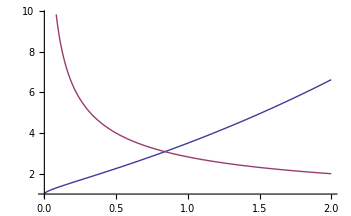

```mathematica
Plot[{ψplot1/k,ψplot2/k}, {En,0, 2}]
```

{{0.844, 3.099}} is the point of intersection.
The x-coordinate gives the energy where the intersection occurs.  Since have ψ_2 = 4/(b k), take the square and the result is (ψ^2)_2 = (16 ℏ^2)/(2 m| E| b^2).  Know from graph that when ℏ, m, and b->1, E=.844, ψ_2=3.099.  So, 3.099^2= (8 ℏ^2)/(m |E| b^2).  Swapping E and 3.099^2yields: E = -(.844 ℏ^2)/(m b^2).  This is a bound state for the double potential function.  

However, this potential setup resembles and attractive potential well with very narrow walls.  So there may be more.  The functions used above were even parity functions, so I will search for other energies using odd functions in the “potential well.”  The odd functions are given by:
ψ_I(x) = Aⅇ^-kx 
ψ_II(x) = B(ⅇ^kx - ⅇ^-kx)  -> B is coefficient because at 0, the coefficients must be equal
ψ_III(x) = -Fⅇ^kx.
I will use the same process again to find some intersections in a numerical analysis.

```mathematica
ψ3:=A ⅇ^(-k x)
ψ4:=B(ⅇ^(k x)-ⅇ^(-k x))
Reduce[ψ3==ψ4,B]
```

(ⅇ^(k x)≠0&&ⅇ^(2 k x)==1&&A==0)||(ⅇ^(k x)≠0&&-1+ⅇ^(2 k x)≠0&&B==A/(-1+ⅇ^(2 k x)))

```mathematica
ψprime2 = D[ψ4,x]-D[ψ3,x]
```

A ⅇ^(-k x) k+B (ⅇ^(-k x) k+ⅇ^(k x) k)

```mathematica
x:=b/2
B:=A/(-1+ⅇ^(2 k x))
ψplot12 = FullSimplify[ψprime2*ⅇ^(k b/2)/k]
```

2 A (1+1/(-1+ⅇ^(b k)))

```mathematica
ψother = (2 m α)/ℏ^2 ψ3
```

(2 A ⅇ^(-(b k)/2) m α)/ℏ^2

```mathematica
α := (2 ℏ^2)/(m b)
ψplot22 = ψother*(ⅇ^((b k)/2))/k
```

(4 A)/(b k)

```mathematica
k:=√((2 m En)/ℏ^2)
m:=1
b:=1
A:=1 
ℏ:=1
```

```mathematica
ψplot12
ψplot22
```

2 (1+1/(-1+ⅇ^(√2 √En)))

(2 √2)/(√En)

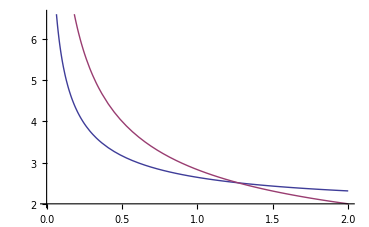

```mathematica
Plot[{ψplot12, ψplot22},{En,0,2}]
```

{{1.273, 2.499}} is the point of intersection.  The x-value is the energy.  Using the same analysis as last time, 2.499^2 = (8 ℏ^2)/(m |E| b^2).  So E = -1.273 ℏ^2/(m b^2).  So the double delta potential does have an odd parity bound state and two total bound states.

### Part B

To find the Transmission and Reflection coefficients of this potential, I must find the propogation matrix.  To solve this, the space will be separated into three regions.  The solutions to the Schrodinger Equation in each region with E>0 are as follows:
ψ_I(x) = Aⅇ^ⅈkx + Bⅇ^-ⅈkx <- V=0
ψ_II(x) = Cⅇ^ιkx + Dⅇ^-ⅈkx <- V = V_1
ψ_III(x) = Fⅇ^ⅈkx + Gⅇ^ⅈkx. <- V = V_2
Employing the boundary conditions yields the results ψ_I(-b/2) = ψ_II(-b/2), ψ_I'(-b/2) = ψ_II'(-b/2) and ψ_II(b/2) = ψ_III(b/2), ψ_II'(b/2) = ψ_III'(b/2).  These results can be set into two systems of linear differential equations relating the coefficients.  These will be used to find the propogation matrix. These matrices are defined below.

```mathematica
N1:=Inverse[{{ⅇ^(-ⅈ k(b/2)),ⅇ^(ⅈ k(b/2))},{ⅈ k ⅇ^(-ⅈ k(b/2)), -ⅈ k ⅇ^(ⅈ k(b/2))}}]
```

```mathematica
N2:={{ⅇ^(-ⅈ k(b/2)),ⅇ^(ⅈ k(b/2))},{ⅈ k ⅇ^(-ⅈ k(b/2)), -ⅈ k ⅇ^(ⅈ k(b/2))}}
```

```mathematica
N3:=Inverse[{{ⅇ^(ⅈ k(b/2)),ⅇ^(-ⅈ k(b/2))},{ⅈ k ⅇ^(ⅈ k(b/2)), -ⅈ k ⅇ^(-ⅈ k(b/2))}} ]
```

```mathematica
N4:={{ⅇ^(ⅈ k(b/2)),ⅇ^(-ⅈ k(b/2))},{ⅈ k ⅇ^(ⅈ k(b/2)), -ⅈ k ⅇ^(-ⅈ k(b/2))}}
```

```mathematica
Prop= N1.N2.N3.N4 //MatrixForm
```

(1 | 0
0 | 1)

The propogation matrix relates the coefficients of ψ_I and ψ_III.  But if the particles are coming from the left, then there is nothing to reflect particles in region III.  Therefore, G goes to zero and A = Prop(1,1)F.  The transmission coefficient is defined by |F/A|^2 = |1/(Prop(1,1))|^2.

```mathematica
one= Part[Prop,1,1,1]
```

1

```mathematica
T = 1/(one^2)
```

1

By the condition that T+R=1, R should be zero. But let’s check.  R = T |B/F|^2 = T Prop(2,1)^2.

```mathematica
two = Part[Prop,1,2,1]
```

0

```mathematica
R = T * two
```

0

So it holds.  This result means that all particles in the incident beam, with E>0, are transmitted through the delta functions.

## Problem 2

Have a two step repulsive potential with V=0 for x<-L, V=V_1 for x>=-L and V_1>0, and V=V_2for x>=0 and V_2> V_1.  All potentials are assumed to be less than the energy of the incident particle.  To solve this, the space will be separated into three regions.  The solutions to the Schrodinger Equation in each region are as follows:
ψ_I(x) = Aⅇ^(ⅈk_I x) + Bⅇ^-ⅈk_Ix
ψ_II(x) = Cⅇ^(ιk_II x) + Dⅇ^-ⅈk_IIx
ψ_III(x) = Fⅇ^(ⅈk_III x) + Gⅇ^(ⅈk_III x). 
Employing the boundary conditions yields the results ψ_I(-L) = ψ_II(-L), ψ_I'(-L) = ψ_II'(-L) and ψ_II(0) = ψ_III(0), ψ_II'(0) = ψ_III'(0).  These results can be set into two systems of linear differential equations relating the coefficients.  These will be used to find the propogation matrix. These matrices are defined below.

```mathematica
M1:=Inverse[{{ⅇ^(-ⅈ Subscript[k, 1] L),ⅇ^(ⅈ Subscript[k, 1] L)},{ⅈ Subscript[k, 1] ⅇ^(-ⅈ Subscript[k, 1] L), -ⅈ Subscript[k, 1] ⅇ^(ⅈ Subscript[k, 1] L)}}]
```

```mathematica
M2:={{ⅇ^(-ⅈ Subscript[k, 2] L),ⅇ^(ⅈ Subscript[k, 2] L)},{ⅈ Subscript[k, 2] ⅇ^(-ⅈ Subscript[k, 2] L), -ⅈ Subscript[k, 2] ⅇ^(ⅈ Subscript[k, 2] L)}}
```

```mathematica
M3:= Inverse[{{1,1},{ⅈ Subscript[k, 2],-ⅈ Subscript[k, 2]}}]
```

```mathematica
M4:= {{1,1},{ⅈ Subscript[k, 3],-ⅈ Subscript[k, 3]}}
```

```mathematica
P=FullSimplify[M1.M2.M3.M4]//MatrixForm
```

((ⅇ^(ⅈ L (k_1-k_2)) (ⅇ^(2 ⅈ L k_2) (k_1-k_2) (k_2-k_3)+(k_1+k_2) (k_2+k_3)))/(4 k_1 k_2) | (ⅇ^(ⅈ L (k_1-k_2)) ((k_1+k_2) (k_2-k_3)+ⅇ^(2 ⅈ L k_2) (k_1-k_2) (k_2+k_3)))/(4 k_1 k_2)
(ⅇ^(-ⅈ L (k_1+k_2)) (ⅇ^(2 ⅈ L k_2) (k_1+k_2) (k_2-k_3)+(k_1-k_2) (k_2+k_3)))/(4 k_1 k_2) | (ⅇ^(-ⅈ L (k_1+k_2)) ((k_1-k_2) (k_2-k_3)+ⅇ^(2 ⅈ L k_2) (k_1+k_2) (k_2+k_3)))/(4 k_1 k_2))

The matrix P, above, relates the coefficients of ψ_I and ψ_III.  Now, assume the beam enters from the left, since there is nothing to cause a reflection in region III, the coefficient, G, goes to zero.  Therefore, A and B are now proportional to only F. A=P(1,1)F and B=P(2,1)F.  The transmission coefficient is defined as |F/A| ^2 = |1/(P(1,1))|^2.

```mathematica
one = Part[P,1,1,1]
```

(ⅇ^(ⅈ L (k_1-k_2)) (ⅇ^(2 ⅈ L k_2) (k_1-k_2) (k_2-k_3)+(k_1+k_2) (k_2+k_3)))/(4 k_1 k_2)

```mathematica
conjone:=(ⅇ^(-ⅈ L (Subscript[k, 1]-Subscript[k, 2])) (ⅇ^(-2 ⅈ L Subscript[k, 2]) (Subscript[k, 1]-Subscript[k, 2]) (Subscript[k, 2]-Subscript[k, 3])+(Subscript[k, 1]+Subscript[k, 2]) (Subscript[k, 2]+Subscript[k, 3])))/(4 Subscript[k, 1] Subscript[k, 2])
```

```mathematica
T =Simplify[(1/(one*conjone))]
```

(16 k_1^2 k_2^2)/((ⅇ^(-2 ⅈ L k_2) (k_1-k_2) (k_2-k_3)+(k_1+k_2) (k_2+k_3)) (ⅇ^(2 ⅈ L k_2) (k_1-k_2) (k_2-k_3)+(k_1+k_2) (k_2+k_3)))

To find the condition where there is no reflection from V_2, I will calculate the condition on V_1that will cause the transmission coefficient | F/C|^2 = 1.  This would mean that nothing reflects from the second potential.  To solve for this, take the product of M3 and M4 above to relate C,D,F, and G.  Then, as last time, set G=0 because of the physical system.  This means that C = M(1,1)F and T = 1/(M(1,1))^2.

```mathematica
prop = M3.M4 //MatrixForm
```

(1/2+k_3/(2 k_2) | 1/2-k_3/(2 k_2)
1/2-k_3/(2 k_2) | 1/2+k_3/(2 k_2))

```mathematica
first = Part[prop,1,1,1]
```

1/2+k_3/(2 k_2)

```mathematica
Subscript[T, Subscript[V, 2]]=Simplify[1/first^2]
```

(4 k_2^2)/(k_2+k_3)^2

Need to solve for T = 1 for V_1 to find the zero reflection condition.

```mathematica
Subscript[k, 2]:=√((2 m (Subscript[V, 1]-En))/ℏ^2)
Subscript[k, 3]:=√((2 m (Subscript[V, 2]-En))/ℏ^2)
Solve[Subscript[T, Subscript[V, 2]]==1,Subscript[V, 1]]
```

{{V_1→V_2},{V_1→1/9 (8 En+V_2)}}

The first answer above where the two potentials are equal is the trivial answer because then there would only be one potential barrier and the problem would be set up very differently.  The second term shows how to set up V_1 with respect to incident energy and V_2 in order to achieve no reflection from V_2.

## Problem 3

The inverse square potential is given by V = βℏ^2/(2m) 1/r^2.  Using the Born approximation, f(θ) = ((-2 m)/kℏ^2)(∫^∞)_0 V Sin[kr] r ⅆr. The differential scattering cross section is given by σ(θ) = |f(θ)|^2.

```mathematica
V:=(β ℏ^2)/(2m) 1/r^2
```

```mathematica
fθ = (-2 m)/(k ℏ^2) Integrate[V Sin[k r] r, {r,0,Infinity}, Assumptions -> {β>0, m>0, ℏ>0, k>0}]
```

-(π β)/(2 k)

```mathematica
fθ^2
```

(π^2 β^2)/(4 k^2)

Another way to solve this problem is to start with the Schrodinger Equation.  The solution to this are the Bessel Functions.  Introduce a new variable that simplifies the constants. The wave function is found to a sinusoidal function.  Since the same wave function with a phase shift is asymptotically the same, can add a phase shift to the argument.  Then solve for the phase shift in terms of the other variables.  Now need to look at the definition of the scattering amplitude, f(θ) = 1/k (Σ_(l=0))^∞ (2l+1) ⅇ^ⅈδ_l Sin[δ_l] P_l (Cos[θ]).  The exponential and Sin terms can be simplified into a single exponential term.  Then, simplified again by Taylor expansion to eliminate exponential terms.  Now, f(θ)=1/k (Σ_(l=0))^∞ (2l+1) δ_l P_l (Cos[θ]).  Plug in for the phase shift solved for previously and the result is f(θ) =-πβ/(2k) (Σ_(l=0))^∞ P_l (Cos[θ]).  The term outside the summation term is the same f(θ) found using the Born approximation.  So to make them equivalent, take the scattering amplitude of S-waves so that l=0 and P_l (Cos[θ]) = 1, resulting in the same answer as above.  So, the S-wave scattering amplitude yields the same result as the Born approximation.

## Problem 4

In order to solve for the S-wave total cross scattering section of a repulsive potential sphere, I need to first solve the Schrodinger equation for the region with the potential:
ⅆ^2/(ⅆ r^2)R + 2/r ⅆ/ⅆrR + (k^2 - (l(l+1))/r^2)R =(2mV)/ℏ^2 R.
Let R(r) = (U(r))/r:
ⅆ^2/(ⅆ r^2)U + (k^2- (l(l+1))/r^2)U = (2mV)/ℏ^2U.
Since we are finding the S-wave scattering cross section, l=0, which leaves the following.
ⅆ^2/(ⅆ r^2)U + k^2U = (2mV)/ℏ^2U.
ⅆ^2/(ⅆ r^2)U + (k^2- (2mV)/ℏ^2)U = 0.
The (2mV)/ℏ^2 remains negative because V is positive. For r > a, the Schrodinger equation is nearly the same as above, only eliminate the second term in the parentheses.  The solutions to these differential equations for r<a and r>a respectively are
U_(r<a)(r) = A_(l=0) Sin[k_insider]
U_(r>a)(r) = B Sin[k_outsider] + F Cos[k_outsider].
Now, the boundary rules must be enforced: U_(r<a)(a) = U_(r>a)(a) and U_(r<a)’(a) = U_(r>a)’(a).

```mathematica
U1 := A Sin[Subscript[k, inside] a]
B := c Cos[Subscript[δ, o]]
F := c Sin[Subscript[δ, o]]
U2 := B Sin[Subscript[k, outside] a] + F Cos[Subscript[k, outside] a]
U1p = D[U1,a]
U2p = FullSimplify[D[U2,a]]
```

A Cos[a k_inside] k_inside

c Cos[a k_outside+δ_o] k_outside

Now I will take the ratios of the functions with their derivatives.

```mathematica
r1 = U1p/U1
```

Cot[a k_inside] k_inside

```mathematica
r2 = FullSimplify[U2p/U2]
```

Cot[a k_outside+δ_o] k_outside

In setting them equal, I need to make an approximation in order to solve for δ_o.  For S-waves, the incident energy, and therefore k_outsidea, is << 1.  So the small angle approximation can be used.  Know that Cotanget is Cos/Sin and Sin[x] = x (approximately) and Cos[x] = 1 (approximately) for small x.  This will only be valid for the incident energy because it is assumed to be small.  This assumption is not made for scattered particle energy.  So, employing this tool and inverting the function yields this result:

```mathematica
new1 := a Subscript[k, outside] + Subscript[δ, o]
new2 := Subscript[k, inside]/Subscript[k, outside] Tan[Subscript[k, inside] a]
```

Now I can solve for δ_o, which is very simple.

```mathematica
Subscript[δ, o] := new2 - a Subscript[k, outside]
```

Now that I have a value for δ_o, I can look at the formula for total scattering cross section.
σ_t = (4π)/k_outside^2 (Σ_(l=0))^∞(2l+1) Sin^2 [δ_l].  Since we are only considering S-waves, I can again set l=0, which leaves this equation: σ_t = (4π)/k_outside^2 Sin^2 [δ_o].  Since incident energy is small, so is the phase shift, δ_o.  Therefore, the small angle approximation can be used in σ_t.

```mathematica
Subscript[σ, t]= FullSimplify[(4π)/Subscript[k, outside]^2 Subscript[δ, o]^2]
```

(4 π (a k_outside^2-k_inside Tan[a k_inside])^2)/k_outside^4

Know the value of k_outside = √(2 mE/ℏ^2) because there is no potential in the region r>a.  Since the potential is positive, have k_inside = √((2m(E-V))/ℏ^2).  Let’s Plug these in:

```mathematica
Subscript[k, outside]:=√(2(m En)/ℏ^2) 
Subscript[k, inside]:= √((2m(En-V))/ℏ^2)
```

```mathematica
FullSimplify[Subscript[σ, t]]
```

(π (-2 a En m+√2 ℏ √m[En-V] Tan[(√2 a √m[En-V])/ℏ])^2)/(En^2 m^2)

As V -> ∞,

```mathematica
Limit[√(c-x), x->-Infinity]
```

∞

This means that the second term in the parentheses goes to ∞.  Let me just play with some algebra and expand.
σ_t = (4π a^2 En m - 4 π a En m ∞ + ∞)/(En^2 m^2) = (4π a^2 En^2 m^2)/(En^2 m^2) - (4π a En m ∞)/(En^2 m^2) + ∞/(En^2 m^2) = 4 πa^2- ∞ + ∞
Since -∞+∞ is indeterminate,

```mathematica
-∞+∞
```

Indeterminate

the total cross scattering section as V -> ∞ is σ_t = 4 πa^2.